-Graphics-

## Lesson 8: Picard’s theorem

-Graphics-

## Overview

In some cases, the existence of a solution to an initial value problem associated with a first-order differential equation can be directly established:

y'(t)=f(t,y(t))

y(t_o)=y_o

Picard’s theorem states that there exists a unique solution to any initial value problem.

To establish the existence and uniqueness of a solution to the initial value problem in general, an indirect method known as Picard’s method is required.

This involves cleverly constructing a sequence of functions that converge to the solution of the initial value problem.

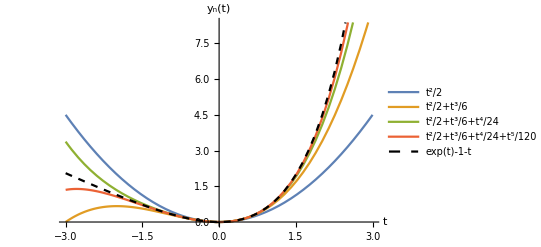

```mathematica
Plot[{Evaluate[Table[Sum[t^(i+1)/Factorial[i+1],{i,1,n}],{n,1,4}]],Exp[t]-1-t},{t,-3,3},]
```

## Transform the Problem

First, consider the equivalent initial value problem centered at the origin:

y'(t)=f(t,y(t))

y(0)=0

According to the fundamental theorem of calculus, y(t) is a solution to the initial value problem if and only if y(t) is a solution to the integral equation:

y(t)=∫_0^t f(s,y(s))ⅆs

Thus, to show the existence and uniqueness of solutions, you must show the existence and uniqueness of the integral equation.

This can be done by constructing a series of functions using Picard’s method.

## Picard’s Method

It is desirable to construct a sequence of functions that will converge to the solution of the integral equation.

To begin, choose an appropriate initial function y_0(t), which in this case will be y_0(t)=0.

The next function is obtained by substituting y_0(t) into the integral equation:

y_1(t)=∫_0^t f(s,y_0(s))ⅆs

Then y_2(t) is obtained in the same way by substituting y_1(t):

y_2(t)=∫_0^t f(s,y_1(s))ⅆs

And for y_n(t):

y_n(t)=∫_0^t f(s,y_(n-1)(s))ⅆs

In general, none of the functions satisfy the integral equation, but the limit of the sequence converges to a solution.

## Picard’s Method Example 1

Solve the initial value problem using Picard’s method:

y'(t)=y(t)+t

y(0)=0

Let the initial function be y_0(t)=0 so that it satisfies the initial condition.

In order to calculate y_1(t), use Integrate:

```mathematica
Integrate[0+s,{s,0,t}]
```

t^2/2

Likewise for y_2(t):

```mathematica
Integrate[s^2/2+s,{s,0,t}]
```

t^2/2+t^3/6

And y_3(t):

```mathematica
Integrate[s^2/2+s^3/6+s,{s,0,t}]
```

t^2/2+t^3/6+t^4/24

## Picard’s Method Example 1

An obvious pattern is beginning to develop where:

y_n(t)=∑_(k=2)^(n+1) t^k/(k !)

As n→∞, the solution converges to the function:

y(t)=t^2/2+t^3/6+t^4/24+... = ∑_(k=2)^∞ t^k/(k !)

The Taylor Series expansion for e^t is:

```mathematica
Series[Exp[t],{t,0,4}]
```

1+t+t^2/2+t^3/6+t^4/24+O[t]^5

Thus the solution found is y(t)=e^t-1-t.

Verify that this function satisfies the integral equation:

```mathematica
Exp[t]-1-t==Integrate[(Exp[s]-1-s)+s,{s,0,t}]
```

True

Also compare this answer to the output from DSolveValue:

```mathematica
DSolveValue[{y'[t]==y[t]+t,y[0]==0},y[t],t]
```

-1+ⅇ^t-t

## Picard’s Method Example 1

View the functions y_n(t) compared to the solution:

```mathematica
Plot[{Evaluate[Table[Sum[t^(i+1)/Factorial[i+1],{i,1,n}],{n,1,4}]],Exp[t]-1-t},{t,-3,3},]
```

-Graphics-

Observe that the functions are converging to the solution.

## Picard’s Method Example 2

Solve the initial value problem using Picard’s method:

y'(t)=-t y(t)-t

y(0)=0

Again, allow the initial function to be y_0(t)=0 so that it satisfies the initial condition.

In order to calculate y_1(t), use Integrate:

```mathematica
Integrate[s*0-s,{s,0,t}]
```

-t^2/2

Likewise for y_2(t):

```mathematica
Integrate[-s(-s^2/2)-s,{s,0,t}]
```

-t^2/2+t^4/8

And y_3(t):

```mathematica
Integrate[-s(-s^2/2+s^4/8)-s,{s,0,t}]
```

-t^2/2+t^4/8-t^6/48

## Picard’s Method Example 2

A pattern is beginning to develop where:

y_n(t)=∑_(k=1)^n (-1)^k t^(2k)/(2^k k !)

As n→∞, the solution converges to the function:

y(t)=t^2/2+t^4/8+t^6/48+... = ∑_(k=1)^∞ (-1)^k t^(2k)/(2^k k !)

Recall that the Taylor Series expansion for e^t is:

```mathematica
series=Series[Exp[t],{t,0,4}]//Normal
```

1+t+t^2/2+t^3/6+t^4/24

Substituting t→-t^2/2, the series expansion being searched for is:

```mathematica
series/.t->-t^2/2
```

1-t^2/2+t^4/8-t^6/48+t^8/384

Thus, the solution is:

y(t)=e^(-t^2/2)-1

Verify that this function satisfies the integral equation:

```mathematica
Exp[-t^2/2]-1==Integrate[-s(Exp[-s^2/2]-1)-s,{s,0,t}]
```

True

Also compare this answer to the output from DSolveValue:

```mathematica
DSolveValue[{y'[t]==-t*y[t]-t,y[0]==0},y[t],t]//Simplify
```

-1+ⅇ^(-t^2/2)

## Picard’s Method Example 2

View the functions y_n(t) compared to the solution:

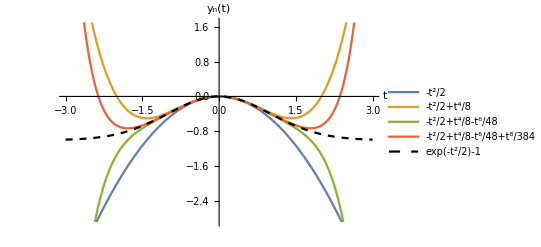

```mathematica
Plot[{Evaluate[Table[Sum[(-1)^i t^(2 i)/(2^i Factorial[i]),{i,1,n}],{n,1,4}]],Exp[-t^2/2]-1},{t,-3,3},]
```

The functions are converging to the solution.

## Picard’s Method Example 3

Solve the initial value problem using Picard’s method:

y'(t)=(y(t))^2+1

y(0)=0

In order to calculate y_1(t), use Integrate:

```mathematica
Integrate[0+1,{s,0,t}]
```

t

Likewise for y_2(t):

```mathematica
Integrate[s^2+1,{s,0,t}]
```

t+t^3/3

And y_3(t):

```mathematica
Integrate[(s+s^3/3)^2+1,{s,0,t}]
```

t+t^3/3+(2 t^5)/15+t^7/63

## Picard’s Method Example 3

This sequence is much less recognizable:

```mathematica
Integrate[(s+s^3/3+(2 s^5)/15+s^7/63)^2+1,{s,0,t}]
```

t+t^3/3+(2 t^5)/15+(17 t^7)/315+(38 t^9)/2835+(134 t^11)/51975+(4 t^13)/12285+t^15/59535

Note that the Taylor Series expansion for Tan is:

```mathematica
Series[Tan[x],{x,0,8}]
```

x+x^3/3+(2 x^5)/15+(17 x^7)/315+O[x]^9

Thus, guess that the solution found is:

y(t)=tan(t)

Verify that this function satisfies the integral equation:

```mathematica
Tan[t]==Integrate[(Tan[s])^2+1,{s,0,t}]
```

ConditionalExpression[True, 2 Re[t]≤π||t∉ℝ]

Also compare this answer to the output from DSolveValue:

```mathematica
DSolveValue[{y'[t]==y[t]^2+1,y[0]==0},y[t],t]
```

Tan[t]

## Picard’s Method Example 3

View the functions y_n(t) compared to the solution:

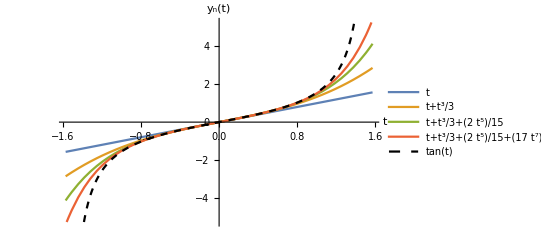

```mathematica
Plot[{Evaluate[Table[Normal[Series[Tan[t],{t,0,i}]],{i,2,8,2}]],Tan[t]},{t,-Pi/2,Pi/2},]
```

The functions are converging to the solution.

## Summary

This lesson discussed a method known as Picard’s method in order to approximate solutions to initial value problems:

y'(t)=f(t,y(t))

y(0)=0

This method involves recursively integrating the derivative:

y_n(t)=∫_0^t f(s,y_(n-1)(s))ⅆs

Through Picard’s method, one is able to prove that there exists a unique solution to any initial value problem associated with a first-order differential equation.